Note: Today is going to consist of a lot of live examples instead of pre-written ones like some other notebooks

## DSolve

### Solving Simple, Ordinary Differential Equations

Lets solve y'[x] + y[x] == a Sin[x]

```mathematica
DSolve[y'[x]+y[x]==a Sin[x],{y},x]
```

{{y→Function[{x},ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])]}}

Now lets give it initial conditions as well
Lets solve y'[x] + y[x] == a Sin[x] 
y[0] = 1

```mathematica
sol=DSolve[{
y'[x]+y[x]==2 Sin[x],
y[0]==1
},{y},x][[1]]
```

{y→Function[{x},-ⅇ^-x (-2+ⅇ^x Cos[x]-ⅇ^x Sin[x])]}

```mathematica
y[x]/.sol
```

-ⅇ^-x (-2+ⅇ^x Cos[x]-ⅇ^x Sin[x])

```mathematica
y[3]/.sol
```

-(-2+ⅇ^3 Cos[3]-ⅇ^3 Sin[3])/ⅇ^3

```mathematica
y[3]/.sol//N
```

1.23069

### Solving Systems of Ordinary Differential Equations

Let’s now look at an example where we want to solve a system of differential equations like:

y’[t] == a y[t] + b x[t] 
x’[t] == c y[t] + d x[t]

```mathematica
sol=DSolve[{
y'[t]==a y[t]+b x[t],
x'[t]== c y[t]+d x[t],
y[0]==1,
x[0]==1
},{x,y},t][[1]]
```

{x→Function[{t},1/(2 √(a^2+4 b c-2 a d+d^2))(a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-2 c ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+2 c ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t))],y→Function[{t},1/(2 √(a^2+4 b c-2 a d+d^2))(-a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-2 b ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+2 b ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t))]}

```mathematica
x[t]/.sol
```

1/(2 √(a^2+4 b c-2 a d+d^2))(a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[1]-(c (ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[2])/(√(a^2+4 b c-2 a d+d^2))

```mathematica
y[t]/.sol
```

-(b (ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[1])/(√(a^2+4 b c-2 a d+d^2))+1/(2 √(a^2+4 b c-2 a d+d^2))(-a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[2]

### More complicated ODEs?

Can we solve this one?
y’[t] == a y[t] + b x[t] + Cos[t]
x’[t] == c y[t] + d x[t] + t

```mathematica
sol=DSolve[{
y'[t]==a y[t]+b x[t]+Cos[t],
x'[t]== c y[t]+d x[t]+t
},{x,y},t][[1]]
```

{x→Function[{t},1/(2 √(a^2+4 b c-2 a d+d^2))(a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[1]-(c (ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[2])/(√(a^2+4 b c-2 a d+d^2))+1/(4 (a^2+4 b c-2 a d+d^2))(a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) (-((16 ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-a^3-3 a b c+a^2 d-b c d+a^2 √(a^2+4 b c-2 a d+d^2)+b c √(a^2+4 b c-2 a d+d^2)+a^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+3 a b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+b c √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 b c t+2 b^2 c^2 t-a^3 d t-3 a b c d t+a^2 d^2 t-a b c √(a^2+4 b c-2 a d+d^2) t+a^2 d √(a^2+4 b c-2 a d+d^2) t-a^2 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-2 b^2 c^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a^3 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+3 a b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-a^2 d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-a b c √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a^2 d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t))/((-a-d+√(a^2+4 b c-2 a d+d^2))^2 (a+d+√(a^2+4 b c-2 a d+d^2))^2))-(4 c ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (4 a+a^3+4 d+3 a^2 d+3 a d^2+d^3+4 √(a^2+4 b c-2 a d+d^2)-a^2 √(a^2+4 b c-2 a d+d^2)-2 a d √(a^2+4 b c-2 a d+d^2)-d^2 √(a^2+4 b c-2 a d+d^2)-a (a^2+4 b c-2 a d+d^2)-d (a^2+4 b c-2 a d+d^2)+(a^2+4 b c-2 a d+d^2)^(3/2)-4 a ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-3 a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-3 a d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+4 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 a d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+(a^2+4 b c-2 a d+d^2)^(3/2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Cos[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)))-(8 c ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-4-2 a^2-4 b c-2 d^2+2 a √(a^2+4 b c-2 a d+d^2)+2 d √(a^2+4 b c-2 a d+d^2)+4 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 a d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 a √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Sin[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2))))-1/(2 (a^2+4 b c-2 a d+d^2))c (ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) ((16 b ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-a^2-2 b c-d^2+a √(a^2+4 b c-2 a d+d^2)+d √(a^2+4 b c-2 a d+d^2)+a^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a b c t-a^2 d t+b c d t-a d^2 t-b c √(a^2+4 b c-2 a d+d^2) t+a d √(a^2+4 b c-2 a d+d^2) t-a b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-b c √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t))/((-a-d+√(a^2+4 b c-2 a d+d^2))^2 (a+d+√(a^2+4 b c-2 a d+d^2))^2)+(4 ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-4 a^2-8 b c+2 a^2 b c+4 a d-a^3 d+4 a b c d-a^2 d^2+2 b c d^2+a d^3+d^4-4 a √(a^2+4 b c-2 a d+d^2)-a^2 d √(a^2+4 b c-2 a d+d^2)-2 a d^2 √(a^2+4 b c-2 a d+d^2)-d^3 √(a^2+4 b c-2 a d+d^2)-2 b c (a^2+4 b c-2 a d+d^2)+a d (a^2+4 b c-2 a d+d^2)-d^2 (a^2+4 b c-2 a d+d^2)+d (a^2+4 b c-2 a d+d^2)^(3/2)+4 a^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+8 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 a^2 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 a d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^3 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 a b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 b c d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a d^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^4 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 a √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 a d^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^3 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 b c (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a d (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d^2 (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (a^2+4 b c-2 a d+d^2)^(3/2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Cos[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)))+(4 ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (4 a-a^3-8 a b c-4 d+3 a^2 d-8 b c d+a d^2-3 d^3+4 √(a^2+4 b c-2 a d+d^2)-a^2 √(a^2+4 b c-2 a d+d^2)+2 a d √(a^2+4 b c-2 a d+d^2)+3 d^2 √(a^2+4 b c-2 a d+d^2)+a (a^2+4 b c-2 a d+d^2)-d (a^2+4 b c-2 a d+d^2)+(a^2+4 b c-2 a d+d^2)^(3/2)-4 a ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+8 a b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+4 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-3 a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+8 b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+3 d^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+4 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 a d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+3 d^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+(a^2+4 b c-2 a d+d^2)^(3/2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Sin[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2))))],y→Function[{t},-(b (ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[1])/(√(a^2+4 b c-2 a d+d^2))+1/(2 √(a^2+4 b c-2 a d+d^2))(-a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) C[2]-1/(2 (a^2+4 b c-2 a d+d^2))b (ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)-ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) (-((16 ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-a^3-3 a b c+a^2 d-b c d+a^2 √(a^2+4 b c-2 a d+d^2)+b c √(a^2+4 b c-2 a d+d^2)+a^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+3 a b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+b c √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 b c t+2 b^2 c^2 t-a^3 d t-3 a b c d t+a^2 d^2 t-a b c √(a^2+4 b c-2 a d+d^2) t+a^2 d √(a^2+4 b c-2 a d+d^2) t-a^2 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-2 b^2 c^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a^3 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+3 a b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-a^2 d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-a b c √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a^2 d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t))/((-a-d+√(a^2+4 b c-2 a d+d^2))^2 (a+d+√(a^2+4 b c-2 a d+d^2))^2))-(4 c ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (4 a+a^3+4 d+3 a^2 d+3 a d^2+d^3+4 √(a^2+4 b c-2 a d+d^2)-a^2 √(a^2+4 b c-2 a d+d^2)-2 a d √(a^2+4 b c-2 a d+d^2)-d^2 √(a^2+4 b c-2 a d+d^2)-a (a^2+4 b c-2 a d+d^2)-d (a^2+4 b c-2 a d+d^2)+(a^2+4 b c-2 a d+d^2)^(3/2)-4 a ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-3 a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-3 a d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+4 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 a d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+(a^2+4 b c-2 a d+d^2)^(3/2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Cos[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)))-(8 c ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-4-2 a^2-4 b c-2 d^2+2 a √(a^2+4 b c-2 a d+d^2)+2 d √(a^2+4 b c-2 a d+d^2)+4 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 a d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 a √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Sin[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2))))+1/(4 (a^2+4 b c-2 a d+d^2))(-a ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+d ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t)+a ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)-d ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)+√(a^2+4 b c-2 a d+d^2) ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t)) ((16 b ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-a^2-2 b c-d^2+a √(a^2+4 b c-2 a d+d^2)+d √(a^2+4 b c-2 a d+d^2)+a^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a b c t-a^2 d t+b c d t-a d^2 t-b c √(a^2+4 b c-2 a d+d^2) t+a d √(a^2+4 b c-2 a d+d^2) t-a b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t-b c √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t+a d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) t))/((-a-d+√(a^2+4 b c-2 a d+d^2))^2 (a+d+√(a^2+4 b c-2 a d+d^2))^2)+(4 ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (-4 a^2-8 b c+2 a^2 b c+4 a d-a^3 d+4 a b c d-a^2 d^2+2 b c d^2+a d^3+d^4-4 a √(a^2+4 b c-2 a d+d^2)-a^2 d √(a^2+4 b c-2 a d+d^2)-2 a d^2 √(a^2+4 b c-2 a d+d^2)-d^3 √(a^2+4 b c-2 a d+d^2)-2 b c (a^2+4 b c-2 a d+d^2)+a d (a^2+4 b c-2 a d+d^2)-d^2 (a^2+4 b c-2 a d+d^2)+d (a^2+4 b c-2 a d+d^2)^(3/2)+4 a^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+8 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 a^2 b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 a d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^3 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 a b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^2 d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 b c d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a d^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^4 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-4 a √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-2 a d^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-d^3 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 b c (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a d (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d^2 (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (a^2+4 b c-2 a d+d^2)^(3/2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Cos[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)))+(4 ⅇ^(-1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) t) (4 a-a^3-8 a b c-4 d+3 a^2 d-8 b c d+a d^2-3 d^3+4 √(a^2+4 b c-2 a d+d^2)-a^2 √(a^2+4 b c-2 a d+d^2)+2 a d √(a^2+4 b c-2 a d+d^2)+3 d^2 √(a^2+4 b c-2 a d+d^2)+a (a^2+4 b c-2 a d+d^2)-d (a^2+4 b c-2 a d+d^2)+(a^2+4 b c-2 a d+d^2)^(3/2)-4 a ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+a^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+8 a b c ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+4 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-3 a^2 d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+8 b c d ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a d^2 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+3 d^3 ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+4 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+2 a d √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+3 d^2 √(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)-a (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+(a^2+4 b c-2 a d+d^2)^(3/2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) Sin[t])/((-2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ-a-d+√(a^2+4 b c-2 a d+d^2)) (-2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2)) (2 ⅈ+a+d+√(a^2+4 b c-2 a d+d^2))))]}

How about this one?

y’[t] == a y[t] + b x[t] + Cos[x[t]]
x’[t] == c y[t] + d x[t] + t

```mathematica
sol=DSolve[{
y'[t]==a y[t]+b x[t]+Cos[x[t]],
x'[t]== c y[t]+d x[t]+t
},{x,y},t][[1]]
```

{y'[t]==Cos[x[t]]+b x[t]+a y[t],x'[t]==t+d x[t]+c y[t]}

Or what about this one?

y'[t]==Sin[ⅇ^y[t]t]

```mathematica
DSolve[{
y'[t]==Sin[ⅇ^y[t] t]
},{y},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[{y'[t]==Sin[ⅇ^y[t] t]},{y},t]

## NDSolve

### Solving Single ODEs Numerically

Let’s see how we can solve y'[t]==Sin[ⅇ^y[t]t] numerically if we know the initial conditions. For instance, let’s say that at time t=0 we know y=1/2 In other words:
y[0]==1/2

```mathematica
sol=NDSolve[{
y'[t]==Sin[ⅇ^y[t] t],
y[0]==1/2
},{y},{t,0,10}][[1]]
```

{y→InterpolatingFunction[…]}

```mathematica
y'[5]/.sol
```

-0.214039

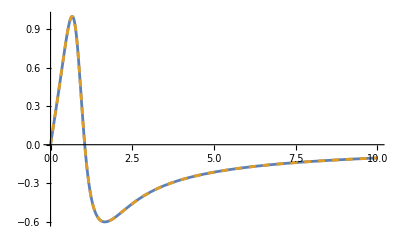

```mathematica
Plot[Evaluate[{y'[t],Sin[ⅇ^y[t] t]}/.sol],{t,0,10},PlotRange->All,PlotStyle->{Automatic,Dashed}]
```

### Initial Conditions in terms of derivatives

What if we had a similar differential equation of the form 

y''[t]==Sin[ⅇ^y'[t]t],
y[0]==1/2,
y'[0]==1/4

```mathematica
NDSolve[{
y''[t]==Sin[ⅇ^y'[t] t],
y[0]==1/2,
y'[0]==1/4
},{y},{t,0,10}]
```

{{y→InterpolatingFunction[…]}}

### Solving Systems of ODEs Numerically

Let’s take a look at this example again 

y’[t] == a y[t] + b x[t] + Cos[x[t]]
x’[t] == c y[t] + d x[t] + t

Where we will assume we know the values of (a | b
c | d) == (1 | -2
2 | 1)
and that (y[0]
x[0]) == (1
0)

```mathematica
sol=NDSolve[{
y'[t]==1 y[t]-2 x[t]+Cos[x[t]],
x'[t]== 2 y[t]+1 x[t]+t,
y[0]==1,
x[0]==0
},{x,y},{t,0,10}][[1]]
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

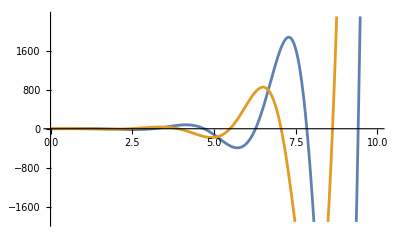

```mathematica
Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,10}]
```

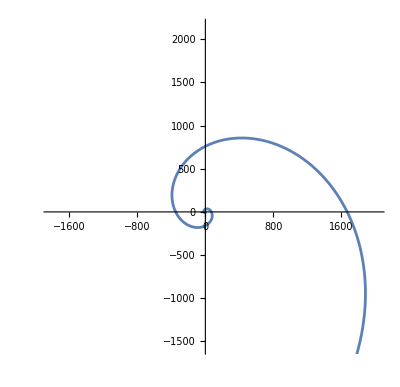

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,10}]
```

### WhenEvents

```mathematica
sol=NDSolve[{
y''[t]==-9.81,
y[0]==5,
y'[0]==0,
WhenEvent[y[t]==0,y'[t]->-0.95 y'[t]]
},y,{t,0,20}][[1]]
```

{y→InterpolatingFunction[…]}

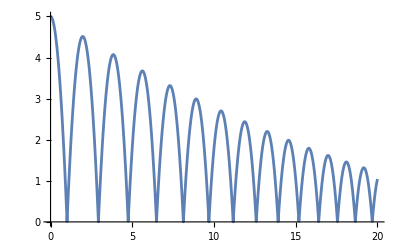

```mathematica
Plot[Evaluate[y[t]/.sol],{t,0,20}]
```